```mathematica
m = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,0,0,0,0},
{1,1,0,1,0,1,0,1,0,0},
{1,1,1,0,1,1,1,0,0,0},
{0,1,0,1,0,1,1,0,0,0},
{0,0,1,1,1,0,1,1,0,0},
{0,0,0,1,1,1,0,0,0,0},
{0,0,1,0,0,1,0,0,1,0},
{0,0,0,0,0,0,0,1,0,1},
{0,0,0,0,0,0,0,0,1,0}}
```

{{0,1,1,1,0,0,0,0,0,0},{1,0,1,1,1,0,0,0,0,0},{1,1,0,1,0,1,0,1,0,0},{1,1,1,0,1,1,1,0,0,0},{0,1,0,1,0,1,1,0,0,0},{0,0,1,1,1,0,1,1,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0}}

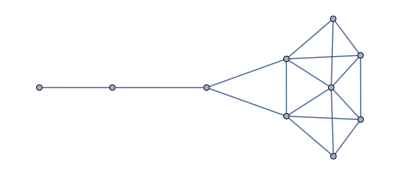

```mathematica
g = AdjacencyGraph[m]
```

```mathematica
DegreeCentrality[g]
```

{3,4,5,6,4,5,3,3,2,1}

```mathematica
BetweennessCentrality[g]
```

```mathematica
ClosenessCentrality[g]
```

```mathematica
EigenvectorCentrality[g]
```

```mathematica
AssortativityCoefficient[g]
```

```mathematica
m=1/2*(m+Transpose[m])
```

{{0,1,1,1,0,0,0,0,0,0},{1,0,1,1,1,0,0,0,0,0},{1,1,0,1,0,1,0,1,0,0},{1,1,1,0,1,1,1,0,0,0},{0,1,0,1,0,1,1,0,0,0},{0,0,1,1,1,0,1,1,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0}}

```mathematica
Eigensystem[m]
```

{{Root4.31Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,7]4.306403794615761,-2,Root-1.87Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,1]-1.868385648816784,Root1.61Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,6]1.6063974126091747,Root-1.46Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,2]-1.4640632817985695,-√2,√2,Root-0.816Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,3]-0.8163750024768371,Root0.640Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,5]0.6403646803511831,Root-0.404Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,4]-0.4043419544839279},{{Root25.6Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,7]25.60498559417212,Root31.6Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,7]31.55077860740179,Root35.6Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,7]35.624970085734,Root43.1Root[8+8 #1-236 #1^2-144 #1^3+650 #1^4-152 #1^5-83 #1^6+2 #1^7&,7]43.08965843068893,Root31.6Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,7]31.55077860740179,Root35.6Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,7]35.624970085734,Root25.6Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,7]25.60498559417212,Root17.5Root[13+51 #1+5 #1^2-101 #1^3-#1^4+61 #1^5-21 #1^6+#1^7&,7]17.545113642281024,Root4.31Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,7]4.306403794615761,1},{0,1,-1,0,-1,1,0,0,0,0},{Root-0.128Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,3]-0.12821391502234517,Root-0.0596Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,3]-0.05959108273740399,Root-1.39Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,1]-1.3927553222946583,Root1.69Root[8+8 #1-236 #1^2-144 #1^3+650 #1^4-152 #1^5-83 #1^6+2 #1^7&,6]1.6918994438384267,Root-0.0596Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,3]-0.05959108273740399,Root-1.39Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,1]-1.3927553222946583,Root-0.128Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,3]-0.12821391502234517,Root2.49Root[13+51 #1+5 #1^2-101 #1^3-#1^4+61 #1^5-21 #1^6+#1^7&,6]2.490864932704515,Root-1.87Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,1]-1.868385648816784,1},{Root-0.319Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,2]-0.3190236949960348,Root-0.518Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,2]-0.5176194425314243,Root0.466Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,5]0.4662670072545718,Root-0.461Root[8+8 #1-236 #1^2-144 #1^3+650 #1^4-152 #1^5-83 #1^6+2 #1^7&,2]-0.46112640292579615,Root-0.518Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,2]-0.5176194425314243,Root0.466Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,5]0.4662670072545718,Root-0.319Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,2]-0.3190236949960348,Root1.58Root[13+51 #1+5 #1^2-101 #1^3-#1^4+61 #1^5-21 #1^6+#1^7&,5]1.5805126472374509,Root1.61Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,6]1.6063974126091747,1},{Root2.13Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,6]2.1326974102062595,Root0.676Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,6]0.6759998502576978,Root-0.105Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,3]-0.10503284643424837,Root-3.69Root[8+8 #1-236 #1^2-144 #1^3+650 #1^4-152 #1^5-83 #1^6+2 #1^7&,1]-3.6933709732933355,Root0.676Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,6]0.6759998502576978,Root-0.105Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,3]-0.10503284643424837,Root2.13Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,6]2.1326974102062595,Root1.14Root[13+51 #1+5 #1^2-101 #1^3-#1^4+61 #1^5-21 #1^6+#1^7&,4]1.1434812931107976,Root-1.46Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,2]-1.4640632817985695,1},{-1,-(-1+√2)/(-2+√2),-(-2+√2)/(2 (-1+√2)),0,-(1-√2)/(-2+√2),-(2-√2)/(2 (-1+√2)),1,0,0,0},{-1,-(1+√2)/(2+√2),-(2+√2)/(2 (1+√2)),0,-(-1-√2)/(2+√2),-(-2-√2)/(2 (1+√2)),1,0,0,0},{Root-0.604Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,1]-0.6036563480134158,Root0.136Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,4]0.13577877209922287,Root0.544Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,6]0.5443310358493704,Root-0.187Root[8+8 #1-236 #1^2-144 #1^3+650 #1^4-152 #1^5-83 #1^6+2 #1^7&,3]-0.18729985534398244,Root0.136Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,4]0.13577877209922287,Root0.544Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,6]0.5443310358493704,Root-0.604Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,1]-0.6036563480134158,Root-0.334Root[13+51 #1+5 #1^2-101 #1^3-#1^4+61 #1^5-21 #1^6+#1^7&,3]-0.3335318553309441,Root-0.816Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,3]-0.8163750024768371,1},{Root0.161Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,4]0.16090543553721795,Root0.412Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,5]0.41217700074749103,Root-0.509Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,2]-0.5090684930470782,Root0.200Root[8+8 #1-236 #1^2-144 #1^3+650 #1^4-152 #1^5-83 #1^6+2 #1^7&,4]0.19992965009414568,Root0.412Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,5]0.41217700074749103,Root-0.509Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,2]-0.5090684930470782,Root0.161Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,4]0.16090543553721795,Root-0.590Root[13+51 #1+5 #1^2-101 #1^3-#1^4+61 #1^5-21 #1^6+#1^7&,2]-0.5899330761587271,Root0.640Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,5]0.6403646803511831,1},{Root1.15Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,5]1.1523055181161967,Root-1.70Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,1]-1.6975237052373733,Root0.371Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,4]0.3712885329380432,Root0.860Root[8+8 #1-236 #1^2-144 #1^3+650 #1^4-152 #1^5-83 #1^6+2 #1^7&,5]0.8603097069416118,Root-1.70Root[1+8 #1-142 #1^2+132 #1^3+676 #1^4-552 #1^5-488 #1^6+16 #1^7&,1]-1.6975237052373733,Root0.371Root[2+11 #1-80 #1^2+6 #1^3+352 #1^4-188 #1^5-280 #1^6+8 #1^7&,4]0.3712885329380432,Root1.15Root[1+5 #1-44 #1^2-172 #1^3+40 #1^4+244 #1^5-112 #1^6+4 #1^7&,5]1.1523055181161967,Root-0.837Root[13+51 #1+5 #1^2-101 #1^3-#1^4+61 #1^5-21 #1^6+#1^7&,1]-0.8365075838441172,Root-0.404Root[-4-10 #1+10 #1^2+28 #1^3+2 #1^4-12 #1^5-2 #1^6+#1^7&,4]-0.4043419544839279,1}}}